```mathematica
Gett2[totrates_]:=Module[{slist,ltotr,R,u,dt},
slist=Insert[Accumulate[totrates],0,1];
ltotr=Length[totrates];(*Length[totrates];*)
R= slist[[-1]];(*Total[totrates];*)
u=RandomReal[{0,1}];
dt = (1/R )*Log[1/u];
dt
];

vars={{1},{2,4},5,100};(*{Ds,Phis,m,tmax}*)
tpar={0.1,0.001,0.001,0.1,0.1,0.1,0.1,0.1};(* JhR,JlL->0 for hole and electron blocking at anode and cathode *)
{kappa,gamma}={0.005,0.005};
BlockInjection={False,True};(*{True,True};*)
Er=0.8;(*10^6*ev/cm * 5nm*)
w0=1;beta=40;(*beta=40 for Temp=0.025; for 300K*)
M=5;wv=0.2;lam=1; (* vibrational assistance for HOMO-LUMO hops*)

AlwaysLP=True;
```

```mathematica
ntraj=5;
maxiter=30;
current={};
gs=Range[1,5,5];(*{0.05,0.1,0.5,1,2}*);
res={};alloutt={};
Do[
Print["================= gg = ",gg,"================="];
alloutx={};
Do[
If[Mod[itraj,5]==0,Print[" traj = ",itraj]];
out=trajectory[5,vars,gg,tpar,kappa,gamma,Er,w0,beta,maxiter,True,BlockInjection,M,wv,lam,AlwaysLP];
$HistoryLength=1;
Print["ZQ: ",Sort[out[[1,All,-1]]//Tally]];
AppendTo[alloutx,out];
,{itraj,1,ntraj}];
AppendTo[alloutt,alloutx];
,{gg,gs}];
```

```mathematica
out[[1,All,-3;;-1]]
```

```mathematica
out[[1,All,7;;8]]
```

```mathematica
current={};
nav=5;
ig=0;
Is={};Ivsg={};Ivsg2={};Ivsg2s={};
charg={};tms={};rc={};times12={};Ivsg3={}
Do[
ig+=1;
alloutx=alloutt[[ig]];
Ix={};chargx={};Ix2={};Ix3={};
tm=0;rcx={};
Do[

{out2,Evst}=alloutx[[itraj]];
charges=out2[[All,3]];
tottime=out2[[-1,2]];
AppendTo[Ix,Total[charges]/tottime];

rates=out2[[All,10]];
tottime2=0;
xx=rates[[All,9;;24]];

AppendTo[Ix3,Total[charges]/Total[Gett2/@rates]];

(*Print[" -----  g= ",gg];
Sort[charges//Tally]//Print;*)

Do[
dts=Gett2/@xx;
tottime2+=Total[dts];
,{ii,1,nav}];
tottime2=tottime2/nav;

(*If[itraj==1,times12x =Gettpm/@xx];
times12x +=Gettpm/@xx;
*)
AppendTo[rcx,Total[Total[xx]]];

AppendTo[Ix2,Total[charges]/tottime2];
AppendTo[chargx,Total[charges]];

tm +=tottime2;
,{itraj,1,ntraj}];

tm=tm/ntraj;

(*AppendTo[times12,times12x/ntraj];*)
AppendTo[rc,{gg,Total[rcx]}];
AppendTo[tms,{gg,tm}];
AppendTo[Is,Ix];
AppendTo[Ivsg,{gg,Total[Ix]}];
AppendTo[Ivsg2,{gg,Total[Ix2]}];
AppendTo[Ivsg3,{gg,Total[Ix3]}];
AppendTo[Ivsg2s,Ix2];
AppendTo[charg,{gg,Total[chargx]}];
,{gg,gs}];
```

{}

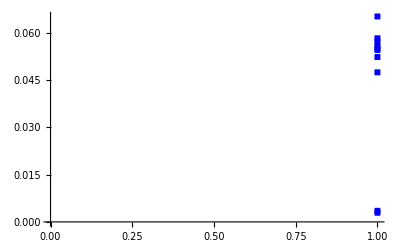

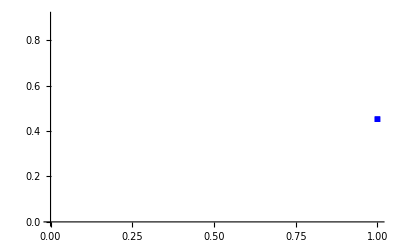

```mathematica
ListPlot[Is//Transpose,Joined->True,PlotMarkers->Style["■", Small, Blue]]
ListPlot[Total[Is//Transpose],Joined->True,PlotMarkers->Style["■", Small, Blue]]
```

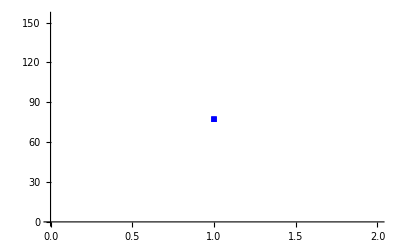

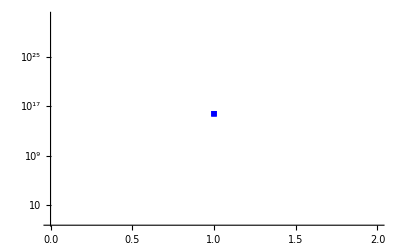

```mathematica
ListPlot[rc,Joined->True,PlotMarkers->Style["■", Small, Blue]]
ListLogPlot[tms,Joined->True,PlotMarkers->Style["■", Small, Blue]]
```

```mathematica
x=Transpose[Ivsg2s];
y=Accumulate[x];
Manipulate[ListPlot[y[[i]]/i,Joined->True,PlotMarkers->{"X"}],{i,1,Length[y],1}]
```

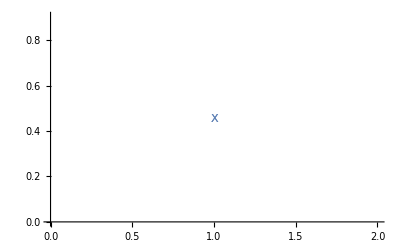

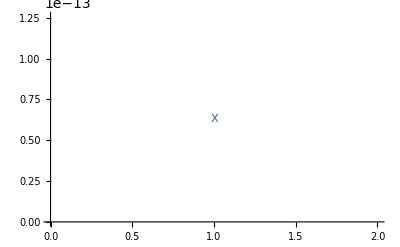

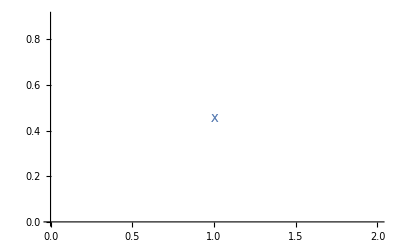

```mathematica
ListPlot[{Ivsg},Joined->True,PlotMarkers->{"X"}]
ListPlot[{Ivsg2},Joined->True,PlotMarkers->{"X"}]
ListPlot[{Ivsg3},Joined->True,PlotMarkers->{"X"}]
```

```mathematica
charg
```

{{1,313}}